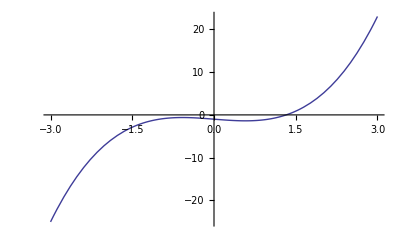

derF= -1+3 x^2

root1 = -0.57735 root2 = 0.57735

derF≠0 - True

B=0.0108318

η=1.80801

K=63.4641

1.24288

False

LessEqual::nord: Invalid comparison with 1.45469  - 1.77315\ ⅈ
 attempted.

1.45469-1.77315 ⅈ≤5.

5.57735

```mathematica
Clear[x];
f=x^3-x-1;
Plot[f,{x,-3,3}]
derF = D[f,x];
Print["derF= ",derF];
roots = Solve[derF ==0,x];
root1 = N[x/.roots[[1]]];
root2= N[x/.roots[[2]]];
Print["root1 = ",root1," root2 = ", root2];
ckeckKantorovichTheorem[f_,segm_]:=(
delta = Abs[segm[[2]]-segm[[1]]]/2;
x0=segm[[2]]-delta;
derF=D[f,x];
derF2 = D[derF,x]; 
x=x0;
Print["derF≠0 - ",derF≠0];
B=Abs[1/derF];
Print["B=",B];
η=Abs[f/derF];
Print["η=",η];
Clear[x];
K=6*Max[Abs[segm[[1]]],Abs[segm[[2]]]];
Print["K=",K];
h = B K η;
Print[h];
Print[h≤1/2];
a = (1 - Sqrt[1 - 2 h])/h*η;
Print[a≤delta];
Return[x0];
);

x0 = ckeckKantorovichTheorem[f,{root2,root2 + 2}]
```

```mathematica
Clear[x];
xn = x0;
Print[x0];
While[Abs[xn - x0] > 0.5 * 10^(-3)  || xn == x0, 
	Clear[x];
x = x0;
	x0 = xn;
	xn = x0 - f/derF;
];
Print[xn]
```

1.57735

3.23547